1.a)  Determine las posiciones en la que aparece por primera vez los decimales consecutivos 2 0 2 2 en
la expansión decimal de π.

```mathematica
pi=Characters[ToString@N[Pi ,1000000]];
pattern = Characters["2022"];
pos=SequencePosition[pi,pattern][[1]];
pos
```

{17954,17957}

1.b)  Realice un histograma de las frecuencias de los primeros 10^5 dígitos de π .Estos ejercicios están
relacionados con un problema abierto de decidir si π es normal o no, es decir si los dígitos del 0 al
9 aparecen igualmente distribuidos.

```mathematica
pi=Characters[ToString@N[Pi ,10^5]];
frequencies = Counts[pi];
frequencies = Delete[frequencies,"."];
BarChart[frequencies,ChartLabels->Automatic,PlotLabel->"PI digits Frequency",AxesLabel->{"Digits","Frequency"}]
```

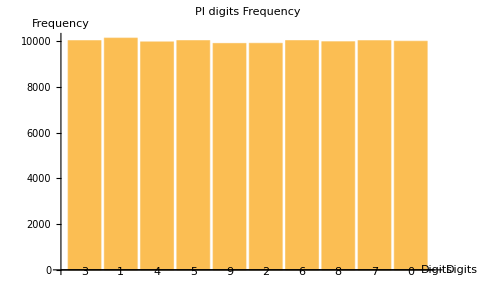

2.  Utilice los comandos Nest y LinearRecurrence para crear dos funciones que generen
el n ́umero de Fibonacci Fn. Compare el tiempo de dos ejecuciones de estas dos funciones para valores
de n = 10 a 1000, tomados de diez en diez. Muestre el análisis con una gráfica.

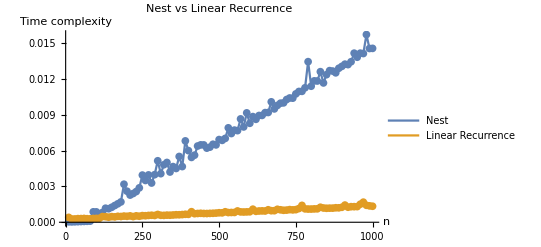

```mathematica
FibNest[n_]:=Nest[{{1,1},{1,0}}.#&,{1,1},n-1][[-1]]
FibLinearRecurrence[n_]:=LinearRecurrence[{1,1},{1,1},n][[-1]]
l1 = {};
l2 = {};
l3 = {};
For[i=10,i<=1000,i+=10;AppendTo[l1,AbsoluteTiming[FibNest[i]][[1]]]];
For[i=10,i<=1000,i+=10;AppendTo[l2,AbsoluteTiming[FibLinearRecurrence[i]][[1]]]];
For[i=10,i<=1000,i+=10,AppendTo[l3,i]];
data1 = Transpose@{l3,l1};
data2 = Transpose@{l3,l2};
ListLinePlot[{data1,data2},Mesh->All,PlotLegends->{"Nest","Linear Recurrence"},PlotLabel->"Nest vs Linear Recurrence"
,AxesLabel->{"n","Time complexity"}]
```